## Quintessence

## Calcularemos las derivadas de las variables dinámicas, los puntos críticos, la matriz Jacobiana o M, y evaluaremos los puntos críticos en dicha matriz.

Este calculo sera tomado para λ constante.

### Calculamos las derivadas de las variables dinámicas

Introducimos las ecuaciones de Friedmann y de campo

```mathematica
FieldEq1=H[t]^2==κ^2/3×(1/2 ×ϵ ×(ϕ'[t])^2+V[ϕ[t]]+ρm[t]);
FieldEq0=H'[t]==-κ^2/2×(ϵ ×(ϕ'[t])^2+(1+wm)× ρm[t]);
FieldEq=ϵ (ϕ''[t]+3×H[t]×ϕ'[t])+D[V[ϕ[t]],ϕ[t]]==0;
```

Introducimos las variables adimensionales

```mathematica
x[t_]:=(κ ×ϕ'[t])/(√6×H[t]);
y[t_]:=(κ ×√V[ϕ[t]])/(√3 ×H[t]);
λ[t_]:=(-D[V[ϕ[t]],ϕ[t]])/(κ×V[ϕ[t]]);
Γ[t_]:=(V[ϕ[t]]×D[V[ϕ[t]],{ϕ[t],2}])/D[V[ϕ[t]],ϕ[t]]^2;
```

Encontramos dx/dN

```mathematica
rules=Solve[{FieldEq0,FieldEq},{H'[t],ϕ''[t]}][[1]];
rules1= Solve[{FieldEq1}, {ρm[t]}][[1]];

Ec1=dxEq=Expand[D[x[t],t]/H[t]/.rules /. rules1 //. {ϕ'[t]->(√6 ×H[t]×xx[t])/κ,D[V[ϕ[t]],ϕ[t]]->-κ ×V[ϕ[t]]×λλ[t],
κ->(√3×H[t]×yy[t])/(√V[ϕ[t]])
}]
```

-(3 xx[t])/2+3/2 wm xx[t]+3/2 ϵ xx[t]^3-3/2 wm ϵ xx[t]^3-3/2 xx[t] yy[t]^2-3/2 wm xx[t] yy[t]^2+(√(3/2) yy[t]^2 λλ[t])/ϵ

Encontramos dy/dN

```mathematica
rules2 =Solve[{FieldEq0},{H'[t] }][[1]];
Ec2=dyEq=Expand[D[y[t],t]/H[t]   /.rules2 /. rules1 //.  {D[V[ϕ[t]],ϕ[t]]->-κ V[ϕ[t]] λλ[t], ϕ'[t]->(√6 ×H[t]×xx[t])/κ, κ->(√3×H[t]yy[t])/(√V[ϕ[t]])} ]
```

(3 yy[t])/2+3/2 wm yy[t]+3/2 ϵ xx[t]^2 yy[t]-3/2 wm ϵ xx[t]^2 yy[t]-(3 yy[t]^3)/2-3/2 wm yy[t]^3-√(3/2) xx[t] yy[t] λλ[t]

Encontramos dλ/dN

```mathematica
Ec3=dλEq=Expand[D[λ[t],t]/H[t]//.{ϕ'[t]->(√6 H[t] xx[t])/κ, D[V[ϕ[t]],{ϕ[t],2}]->(ΓΓ[t]×(D[V[ϕ[t]],ϕ[t]])^2)/V[ϕ[t]], D[V[ϕ[t]],ϕ[t]]->-κ V[ϕ[t]] λλ[t] } ]
```

√6 xx[t] λλ[t]^2-√6 xx[t] ΓΓ[t] λλ[t]^2

Encontramos los puntos críticos si ϵ =+1

```mathematica
Ec1=-3 x+(√6)/2 λ y^2+3/2 x ((1-wm) x^2+(1+wm) (1-y^2))==0;
Ec2=-(√6)/2 λ x y+3/2 y ((1-wm) x^2+(1+wm) (1-y^2))==0;


(*Resolvemos las ecuaciones para x e y*)
PuntosCriticos=Solve[{Ec1,Ec2},{x,y}];
Simplify[PuntosCriticos]
```

{{x→-1,y→0},{x→0,y→0},{x→1,y→0},{x→(√(3/2) (1+wm))/λ,y→-(√(3/2) √(1-wm^2))/λ},{x→(√(3/2) (1+wm))/λ,y→(√(3/2) √(1-wm^2))/λ},{x→λ/(√6),y→-√(1-λ^2/6)},{x→λ/(√6),y→√(1-λ^2/6)}}

### Construimos la matriz Jacobiana “M”

```mathematica
f[x_,y_]:=-3 x+(√6)/2 λ y^2+3/2 x ((1-wm) x^2+(1+wm) (1-y^2));
g[x_,y_]:=-(√6)/2 λ x y+3/2 y ((1-wm) x^2+(1+wm) (1-y^2));

M={{D[f[x,y],x],D[f[x,y],y]},{D[g[x,y],x],D[g[x,y],y]}};	MM=M//MatrixForm
```

(-3+3 (1-wm) x^2+3/2 ((1-wm) x^2+(1+wm) (1-y^2)) | -3 (1+wm) x y+√6 y λ
3 (1-wm) x y-√(3/2) y λ | -3 (1+wm) y^2+3/2 ((1-wm) x^2+(1+wm) (1-y^2))-√(3/2) x λ)

### Hallamos los eigenvalores de la matriz Jacobiana

Para hallar los eigenvalores primero tenemos que reemplazar el valor de los puntos criticos hallados anteriormente y reemplazarlo en la matriz Jacobiana o M y después de eso recién podremos hallar dichos eigenvalores

#### Para el primer punto crítico {x→-1,y→0}

```mathematica
test=PuntosCriticos[[1]]

Mf=Simplify[Simplify[M]/.test];
Simplify[Eigenvalues[Mf]];
Solve[CharacteristicPolynomial[Mf,u]==0,u]
```

{x→-1,y→0}

{{u→-3 (-1+wm)},{u→1/2 (6+√6 λ)}}

#### Para el segundo punto crítico {x→0,y→0}

```mathematica
test=PuntosCriticos[[2]]

Mf=Simplify[Simplify[M]/.test];
Simplify[Eigenvalues[Mf]];
Solve[CharacteristicPolynomial[Mf,u]==0,u]
```

{x→0,y→0}

{{u→3/2 (-1+wm)},{u→(3 (1+wm))/2}}

#### Para el tercer punto crítico {x→1,y→0}

```mathematica
test=PuntosCriticos[[3]]

Mf=Simplify[Simplify[M]/.test];
Simplify[Eigenvalues[Mf]];
Solve[CharacteristicPolynomial[Mf,u]==0,u]
```

{x→1,y→0}

{{u→-3 (-1+wm)},{u→1/2 (6-√6 λ)}}

#### Para el cuarto punto crítico {x→(√(3/2) (1+wm))/λ,y→(√(3/2) √(1-wm^2))/λ}

```mathematica
test=PuntosCriticos[[5]]

Mf=Simplify[Simplify[M]/.test];
Simplify[Eigenvalues[Mf]];
Solve[CharacteristicPolynomial[Mf,u]==0,u]
```

{x→(√(3/2) (1+wm))/λ,y→(√(3/2) √(1-wm^2))/λ}

{{u→3/4 (-1+wm-(√(24+24 wm-24 wm^2-24 wm^3-7 λ^2-2 wm λ^2+9 wm^2 λ^2))/λ)},{u→3/4 (-1+wm+(√(24+24 wm-24 wm^2-24 wm^3-7 λ^2-2 wm λ^2+9 wm^2 λ^2))/λ)}}

#### Para el quinto punto crítico {x→λ/(√6),y→√(1-λ^2/6)}}

```mathematica
test=PuntosCriticos[[7]]

Mf=Simplify[Simplify[M]/.test];
Simplify[Eigenvalues[Mf]];
Solve[CharacteristicPolynomial[Mf,u]==0,u]
```

{x→λ/(√6),y→(√(6-λ^2))/(√6)}

{{u→1/2 (-6+λ^2)},{u→-3-3 wm+λ^2}}

### Hallamos la estabilidad de los eigenvalores

(*Para ello utilizamos el comando reduce*)

```mathematica
{x->0,y->0} 
Reduce[3/2 (-1+wm)<0 && (3 (1+wm))/2<0]
Reduce[3/2 (-1+wm)>0 && (3 (1+wm))/2>0]
Reduce[3/2 (-1+wm)>0 && (3 (1+wm))/2<0]
Reduce[3/2 (-1+wm)<0 && (3 (1+wm))/2>0]
```

{x→0,y→0}

wm<-1

wm>1

False

-1<wm<1

```mathematica
{x->1,y->0}
Reduce[-3 (-1+wm)<0 && 1/2 (6-√6 λ)<0]
Reduce[-3 (-1+wm)>0 && 1/2 (6-√6 λ)>0]
Reduce[-3 (-1+wm)>0 && 1/2 (6-√6 λ)<0]
Reduce[-3 (-1+wm)<0 && 1/2 (6-√6 λ)>0]
```

{x→1,y→0}

wm>1&&λ>√6

wm<1&&λ<√6

wm<1&&λ>√6

wm>1&&λ<√6

```mathematica
{x->-1,y->0}
Reduce[-3 (-1+wm)<0 && 1/2 (6+√6 λ)<0]
Reduce[-3 (-1+wm)>0 && 1/2 (6+√6 λ)>0]
Reduce[-3 (-1+wm)>0 && 1/2 (6+√6 λ)<0]
Reduce[-3 (-1+wm)<0 && 1/2 (6+√6 λ)>0]
```

{x→-1,y→0}

wm>1&&λ<-√6

wm<1&&λ>-√6

wm<1&&λ<-√6

wm>1&&λ>-√6

```mathematica
{x->λ/(√6),y->√(1-λ^2/6)}
(*Hemos considerado que λ^2 se exprese como λ2*)
Reduce[1/2 (-6+λ2)<0&& -3-3 wm+λ2<0]
Reduce[1/2 (-6+λ2)>0&& -3-3 wm+λ2>0]
Reduce[1/2 (-6+λ2)>0&& -3-3 wm+λ2<0]
Reduce[1/2 (-6+λ2)<0&& -3-3 wm+λ2>0]
```

{x→λ/(√6),y→√(1-λ^2/6)}

(wm≤1&&λ2<3+3 wm)||(wm>1&&λ2<6)

(wm≤1&&λ2>6)||(wm>1&&λ2>3+3 wm)

wm>1&&6<λ2<3+3 wm

wm<1&&3+3 wm<λ2<6

```mathematica
{x->(√(3/2) (1+wm))/λ,y->(√(3/2) √(1-wm^2))/λ}
(*Hemos considerado que λ^2,wm^2 y wm^3 se expresen como λ2, wm2 y wm3 respectivamente*)

Reduce[3/4 (-1+wm-(√(24+24 wm-24 wm2-24 wm3-7 λ2-2 wm λ2+9 wm2 λ2))/λ)<0&& 3/4 (-1+wm+(√(24+24 wm-24 wm2-24 wm3-7 λ2-2 wm λ2+9 wm2 λ2))/λ)<0]
Reduce[3/4 (-1+wm-(√(24+24 wm-24 wm2-24 wm3-7 λ2-2 wm λ2+9 wm2 λ2))/λ)>0&& 3/4 (-1+wm+(√(24+24 wm-24 wm2-24 wm3-7 λ2-2 wm λ2+9 wm2 λ2))/λ)>0]
Reduce[3/4 (-1+wm-(√(24+24 wm-24 wm2-24 wm3-7 λ2-2 wm λ2+9 wm2 λ2))/λ)>0&& 3/4 (-1+wm+(√(24+24 wm-24 wm2-24 wm3-7 λ2-2 wm λ2+9 wm2 λ2))/λ)<0]
Reduce[3/4 (-1+wm-(√(24+24 wm-24 wm2-24 wm3-7 λ2-2 wm λ2+9 wm2 λ2))/λ)<0&& 3/4 (-1+wm+(√(24+24 wm-24 wm2-24 wm3-7 λ2-2 wm λ2+9 wm2λ2))/λ)>0]
```

{x→(√(3/2) (1+wm))/λ,y→(√(3/2) √(1-wm^2))/λ}

(wm2|λ|λ2)∈ℝ&&λ≠0&&wm<1&&1/24 (24+24 wm-24 wm2-λ^2+2 wm λ^2-wm^2 λ^2-7 λ2-2 wm λ2+9 wm2 λ2)<wm3≤1/24 (24+24 wm-24 wm2-7 λ2-2 wm λ2+9 wm2 λ2)

(wm2|λ|λ2)∈ℝ&&λ≠0&&wm>1&&1/24 (24+24 wm-24 wm2-λ^2+2 wm λ^2-wm^2 λ^2-7 λ2-2 wm λ2+9 wm2 λ2)<wm3≤1/24 (24+24 wm-24 wm2-7 λ2-2 wm λ2+9 wm2 λ2)

(wm|wm2|λ2)∈ℝ&&λ<0&&wm3<1/24 (24+24 wm-24 wm2-λ^2+2 wm λ^2-wm^2 λ^2-7 λ2-2 wm λ2+9 wm2 λ2)

(wm2|λ2)∈ℝ&&λ>0&&((wm<1&&wm3≤1/24 (24+24 wm-24 wm2-7 λ2-2 wm λ2+9 wm2 λ2)&&wm2λ2>1/9 (-24-24 wm+24 wm2+24 wm3+λ^2-2 wm λ^2+wm^2 λ^2+7 λ2+2 wm λ2))||(wm==1&&wm3<1/24 (48-24 wm2-9 λ2+9 wm2 λ2)&&wm2λ2>1/9 (-48+24 wm2+24 wm3+9 λ2))||(wm>1&&wm3<1/24 (24+24 wm-24 wm2-λ^2+2 wm λ^2-wm^2 λ^2-7 λ2-2 wm λ2+9 wm2 λ2)&&wm2λ2≥1/9 (-24-24 wm+24 wm2+24 wm3+7 λ2+2 wm λ2)))

```mathematica
{x->(√(3/2) (1+wm))/λ,y->(√(3/2) √(1-wm^2))/λ}

3/4(1-wm)(1-√((24(1+2wm+wm2)-λ2(9wm-7))/(λ2(1-wm))));

Reduce[3/4(1-wm)(1+√((24(1+2wm+wm2)-λ2(9wm-7))/(λ2(1-wm))))<0 && 3/4(1-wm)(1-√((24(1+2wm+wm2)-λ2(9wm-7))/(λ2(1-wm))))<0]
Reduce[3/4(1-wm)(1+√((24(1+2wm+wm2)-λ2(9wm-7))/(λ2(1-wm))))>0 && 3/4(1-wm)(1-√((24(1+2wm+wm2)-λ2(9wm-7))/(λ2(1-wm))))>0]
Reduce[3/4(1-wm)(1+√((24(1+2wm+wm2)-λ2(9wm-7))/(λ2(1-wm))))>0 && 3/4(1-wm)(1-√((24(1+2wm+wm2)-λ2(9wm-7))/(λ2(1-wm))))<0]
Reduce[3/4(1-wm)(1+√((24(1+2wm+wm2)-λ2(9wm-7))/(λ2(1-wm))))<0 &&3/4(1-wm)(1-√((24(1+2wm+wm2)-λ2(9wm-7))/(λ2(1-wm))))>0]
```

{x→(√(3/2) (1+wm))/λ,y→(√(3/2) √(1-wm^2))/λ}

(wm2≤-3&&((36+12 wm2<λ2<0&&(24+24 wm2+7 λ2)/(-48+9 λ2)≤wm<(12+12 wm2+3 λ2)/(-24+4 λ2))||(0<λ2<16/3&&(12+12 wm2+3 λ2)/(-24+4 λ2)<wm≤(24+24 wm2+7 λ2)/(-48+9 λ2))||(16/3≤λ2<6&&wm>(12+12 wm2+3 λ2)/(-24+4 λ2))))||(-3<wm2≤-23/9&&((36+12 wm2<λ2<16/3&&(12+12 wm2+3 λ2)/(-24+4 λ2)<wm≤(24+24 wm2+7 λ2)/(-48+9 λ2))||(16/3≤λ2<6&&wm>(12+12 wm2+3 λ2)/(-24+4 λ2))))||(-23/9<wm2<-5/2&&((16/3<λ2<36+12 wm2&&wm≥(24+24 wm2+7 λ2)/(-48+9 λ2))||(λ2==36+12 wm2&&wm>(24+24 wm2+7 λ2)/(-48+9 λ2))||(36+12 wm2<λ2<6&&wm>(12+12 wm2+3 λ2)/(-24+4 λ2))))||(wm2==-5/2&&16/3<λ2<6&&wm≥(-36+7 λ2)/(-48+9 λ2))||(wm2>-5/2&&((16/3<λ2≤6&&wm≥(24+24 wm2+7 λ2)/(-48+9 λ2))||(6<λ2<36+12 wm2&&(24+24 wm2+7 λ2)/(-48+9 λ2)≤wm<(12+12 wm2+3 λ2)/(-24+4 λ2))))

(wm2≤-3&&((λ2<36+12 wm2&&(12+12 wm2+3 λ2)/(-24+4 λ2)<wm≤(24+24 wm2+7 λ2)/(-48+9 λ2))||(16/3<λ2≤6&&wm≤(24+24 wm2+7 λ2)/(-48+9 λ2))||(λ2>6&&(12+12 wm2+3 λ2)/(-24+4 λ2)<wm≤(24+24 wm2+7 λ2)/(-48+9 λ2))))||(-3<wm2<-23/9&&((λ2<0&&(12+12 wm2+3 λ2)/(-24+4 λ2)<wm≤(24+24 wm2+7 λ2)/(-48+9 λ2))||(0<λ2<36+12 wm2&&(24+24 wm2+7 λ2)/(-48+9 λ2)≤wm<(12+12 wm2+3 λ2)/(-24+4 λ2))||(16/3<λ2≤6&&wm≤(24+24 wm2+7 λ2)/(-48+9 λ2))||(λ2>6&&(12+12 wm2+3 λ2)/(-24+4 λ2)<wm≤(24+24 wm2+7 λ2)/(-48+9 λ2))))||(wm2==-23/9&&((λ2<0&&(-56/3+3 λ2)/(-24+4 λ2)<wm≤(-112/3+7 λ2)/(-48+9 λ2))||(0<λ2<16/3&&(-112/3+7 λ2)/(-48+9 λ2)≤wm<(-56/3+3 λ2)/(-24+4 λ2))||(wm<1&&λ2==16/3)||(16/3<λ2≤6&&wm≤(-112/3+7 λ2)/(-48+9 λ2))||(λ2>6&&(-56/3+3 λ2)/(-24+4 λ2)<wm≤(-112/3+7 λ2)/(-48+9 λ2))))||(-23/9<wm2<-5/2&&((λ2<0&&(12+12 wm2+3 λ2)/(-24+4 λ2)<wm≤(24+24 wm2+7 λ2)/(-48+9 λ2))||(0<λ2<16/3&&(24+24 wm2+7 λ2)/(-48+9 λ2)≤wm<(12+12 wm2+3 λ2)/(-24+4 λ2))||(16/3≤λ2<36+12 wm2&&wm<(12+12 wm2+3 λ2)/(-24+4 λ2))||(λ2==36+12 wm2&&wm<(24+24 wm2+7 λ2)/(-48+9 λ2))||(36+12 wm2<λ2≤6&&wm≤(24+24 wm2+7 λ2)/(-48+9 λ2))||(λ2>6&&(12+12 wm2+3 λ2)/(-24+4 λ2)<wm≤(24+24 wm2+7 λ2)/(-48+9 λ2))))||(wm2≥-5/2&&((λ2<0&&(12+12 wm2+3 λ2)/(-24+4 λ2)<wm≤(24+24 wm2+7 λ2)/(-48+9 λ2))||(0<λ2<16/3&&(24+24 wm2+7 λ2)/(-48+9 λ2)≤wm<(12+12 wm2+3 λ2)/(-24+4 λ2))||(16/3≤λ2<6&&wm<(12+12 wm2+3 λ2)/(-24+4 λ2))||(λ2>36+12 wm2&&(12+12 wm2+3 λ2)/(-24+4 λ2)<wm≤(24+24 wm2+7 λ2)/(-48+9 λ2))))

(wm2<-3&&((λ2≤36+12 wm2&&wm<(12+12 wm2+3 λ2)/(-24+4 λ2))||(wm<1&&36+12 wm2<λ2<0)||(λ2>6&&wm<(12+12 wm2+3 λ2)/(-24+4 λ2))))||(-3≤wm2≤-5/2&&((λ2<0&&wm<(12+12 wm2+3 λ2)/(-24+4 λ2))||(0<λ2<36+12 wm2&&(12+12 wm2+3 λ2)/(-24+4 λ2)<wm<1)||(λ2>6&&wm<(12+12 wm2+3 λ2)/(-24+4 λ2))))||(wm2>-5/2&&((λ2<0&&wm<(12+12 wm2+3 λ2)/(-24+4 λ2))||(0<λ2<6&&(12+12 wm2+3 λ2)/(-24+4 λ2)<wm<1)||(wm<1&&6≤λ2≤36+12 wm2)||(λ2>36+12 wm2&&wm<(12+12 wm2+3 λ2)/(-24+4 λ2))))

(wm2<-3&&((wm>1&&(λ2≤36+12 wm2||λ2≥6))||(36+12 wm2<λ2<0&&wm>(12+12 wm2+3 λ2)/(-24+4 λ2))||(0<λ2<6&&1<wm<(12+12 wm2+3 λ2)/(-24+4 λ2))))||(-3≤wm2<-5/2&&((wm>1&&(λ2<0||λ2≥6))||(36+12 wm2<λ2<6&&1<wm<(12+12 wm2+3 λ2)/(-24+4 λ2))))||(wm>1&&wm2==-5/2&&(λ2<0||λ2>6))||(wm2>-5/2&&((wm>1&&(λ2<0||λ2≥36+12 wm2))||(6<λ2<36+12 wm2&&wm>(12+12 wm2+3 λ2)/(-24+4 λ2))))

### Gráfica de la evolución del sistema

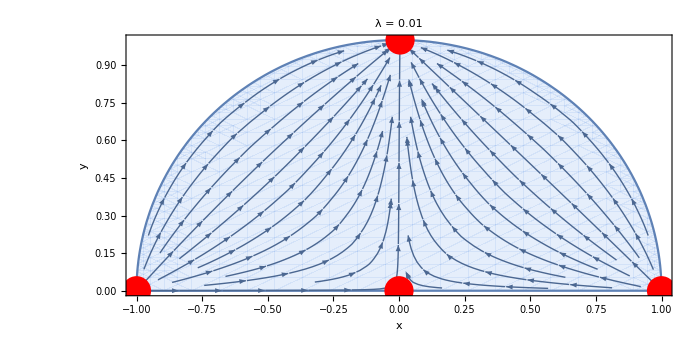

```mathematica
(*Definimos los parámetros*)
parameterValues={λ->0.01,wm->0};

(*Definir puntos críticos*)
points={{0,0},{-1,0},{1,0},{λ/(√6),(√(6-λ^2))/(√6)}/. parameterValues,{(√(3/2) (1+wm))/λ,(√(3/2) (1+wm))/λ}/. parameterValues};
(*Gráfico de los puntos críticos*)
criticalPointsPlot=ListPlot[points,PlotStyle->{Red,PointSize[0.03]},PlotRange->All];

(*Campo vectorial*)
vectorField0=
StreamPlot[{-3 x+(√6)/2 λ y^2+3/2 x ((1-wm) x^2+(1+wm) (1-y^2)),-(√6)/2 λ x y+3/2 y ((1-wm) x^2+(1+wm) (1-y^2))}/. parameterValues,{x,-1,1},{y,0,1},StreamColorFunction->None,RegionFunction->Function[{x,y},x^2+y^2<1],AspectRatio->1/2,FrameLabel->{Style["x",Large,Black],Style["y",Large,Black]},FrameStyle->Directive[Bold,18],PlotLabel->Style[StringJoin[{"λ = ",ToString[λ/. parameterValues]}],Large,Black]];

(*Combinar gráficos*)
dib=Show[vectorField0,criticalPointsPlot,ImageSize->700,ImageResolution->700]
```

### Solución Numérica

{{0.679629,0.320371}}

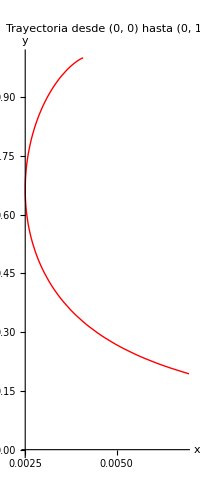

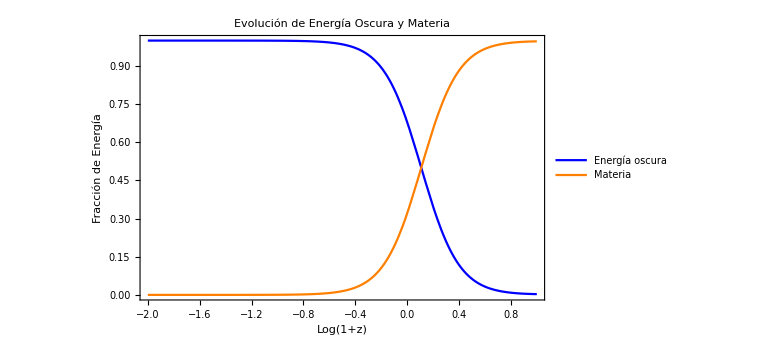

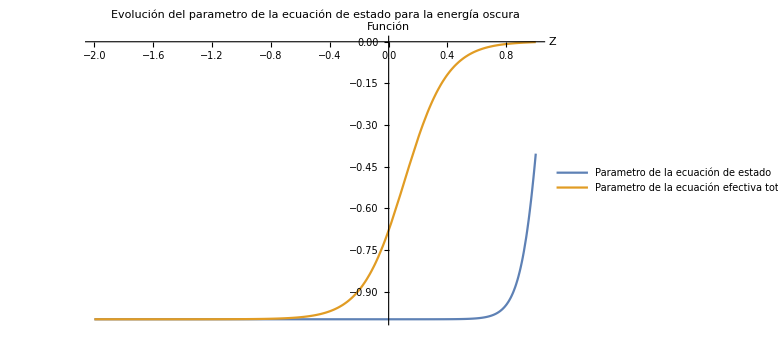

```mathematica
parameterValues={λ->0.01,wm->0};

(*Cambiamos el factor de escala*)
(*N=log(a)=log(1/(1-z))*)
 solucion =NDSolve[{
x'[Z]==-(Log[10](-3 x[Z]+(√6)/2 λ y[Z]^2+3/2 x[Z] ((1-wm) x[Z]^2+(1+wm) (1-y[Z]^2))))/. parameterValues,
y'[Z]==-(Log[10](-(√6)/2 λ x [Z]y[Z]+3/2 y[Z]((1-wm) x[Z]^2+(1+wm) (1-y[Z]^2))))/. parameterValues,
x[1]==0.03,y[1]==0.046},{x,y},{Z,1,-2}];
(*x[1] e y[1] es debido a que queremos trabajar en la epoca de materia*)
Evaluate[{x[0]^2+y[0]^2,1-x[0]^2-y[0]^2}/. solucion]

(*Gráfico de la trayectoria en el plano xy*)
trayectoria=ParametricPlot[Evaluate[{x[Z],y[Z]}/. solucion],{Z,1,-2},PlotStyle->{Thick,Red},AxesLabel->{"x","y"},PlotLabel->"Trayectoria desde (0, 0) hasta (0, 1)"];

(*Mostrar la gráfica*)
trayectoria

(*Densidad fraccionaria para la energia oscura y para la materia*)
Plot[Evaluate[{x[Z]^2+y[Z]^2,1-x[Z]^2-y[Z]^2}/. solucion], {Z,-2,1}, PlotStyle->{Blue, Orange},PlotLegends->{"Energía oscura","Materia"},AxesLabel->{"Z","Fracción"},PlotLabel->"Evolución de Energía Oscura y Materia",Frame->True,FrameLabel->{"Log(1+z)","Fracción de Energía"},ImageSize->Large ]

Plot[Evaluate[{(x[Z]^2-y[Z]^2)/(x[Z]^2+y[Z]^2), wm+(1-wm)*x[Z]^2-(1+wm)*y[Z]^2}/. solucion/. parameterValues],{Z,-2,1},PlotStyle->Thick,PlotLegends->{"Parametro de la ecuación de estado","Parametro de la ecuación efectiva total"}, AxesLabel->{"Z","Función"},PlotLabel->"Evolución del parametro de la ecuación de estado para la energía oscura",ImageSize->Large]
```

### Hallamos el atractor

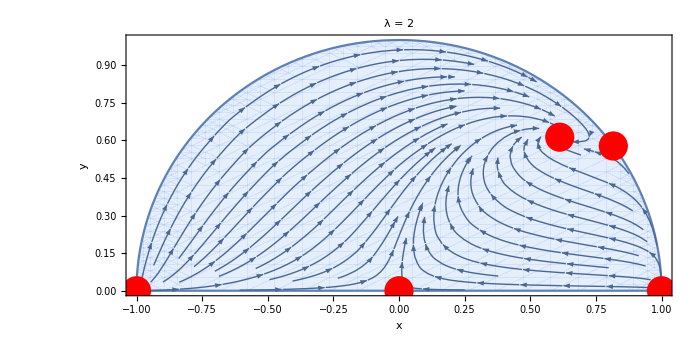

```mathematica
(*Definimos los parámetros*)
parameterValues={λ->2,wm->0};

(*Definir puntos críticos*)
points={{0,0},{-1,0},{1,0},{λ/(√6),(√(6-λ^2))/(√6)}/. parameterValues,{(√(3/2) (1+wm))/λ,(√(3/2) (1+wm))/λ}/. parameterValues};
(*Gráfico de los puntos críticos*)
criticalPointsPlot=ListPlot[points,PlotStyle->{Red,PointSize[0.03]},PlotRange->All];

(*Campo vectorial*)
vectorField0=
StreamPlot[{-3 x+(√6)/2 λ y^2+3/2 x ((1-wm) x^2+(1+wm) (1-y^2)),-(√6)/2 λ x y+3/2 y ((1-wm) x^2+(1+wm) (1-y^2))}/. parameterValues,{x,-1,1},{y,0,1},StreamColorFunction->None,RegionFunction->Function[{x,y},x^2+y^2<1],AspectRatio->1/2,FrameLabel->{Style["x",Large,Black],Style["y",Large,Black]},FrameStyle->Directive[Bold,18],PlotLabel->Style[StringJoin[{"λ = ",ToString[λ/. parameterValues]}],Large,Black]];

(*Combinar gráficos*)
dib=Show[vectorField0,criticalPointsPlot,ImageSize->700,ImageResolution->700]
```